URLRead::invhttp: 
   Operation timed out after 10000 milliseconds with 0 bytes received.

General::ChatbookInternal: 
   An unexpected error occurred. 
    Hyperlink[Report this issue », 
     https://github.com/WolframResearch/Chatbook/issues/new?title=Insert+Title
       +Here&labels=bug&body=Descr<<2959>>State%0AcatchTop%0A%60%60%60%0A%0A%3
       C%2Fdetails%3E]

```mathematica
DHRotation[theta_,alpha_]:={{Cos[theta], -Sin[theta]Cos[alpha], Sin[theta]Sin[alpha]}, {Sin[theta], Cos[theta]Cos[alpha], -Cos[theta]Sin[alpha]}, {0, Sin[alpha], Cos[alpha]}};
DHDisplacement[theta_,d_,a_]:={{a*Cos[theta]}, {a*Sin[theta]}, {d}};
DHTransform[theta_,alpha_,d_,a_]:=ArrayFlatten[{{DHRotation[theta,alpha],DHDisplacement[theta,d,a]},{0,1}}];
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x});
```

#### Getting the H matrix of the end effector to the base

```mathematica
Heto4 = DHTransform[th5-(Pi/2),0,0,L6]
H4to3 = DHTransform[th4,Pi/2,-L5,0]
H3to2 = DHTransform[th3,0,0,L4]
H2to1 = DHTransform[0,-Pi/2,d2,L3]
H1to0 = DHTransform[0,Pi/2,d1,0]

Heto0 = H1to0.H2to1.H3to2.H4to3.Heto4;
Heto0 //FullSimplify // MatrixForm
```

{{Sin[th5],Cos[th5],0,L6 Sin[th5]},{-Cos[th5],Sin[th5],0,-L6 Cos[th5]},{0,0,1,0},{0,0,0,1}}

{{Cos[th4],0,Sin[th4],0},{Sin[th4],0,-Cos[th4],0},{0,1,0,-L5},{0,0,0,1}}

{{Cos[th3],-Sin[th3],0,L4 Cos[th3]},{Sin[th3],Cos[th3],0,L4 Sin[th3]},{0,0,1,0},{0,0,0,1}}

{{1,0,0,L3},{0,0,1,0},{0,-1,0,d2},{0,0,0,1}}

{{1,0,0,0},{0,0,-1,0},{0,1,0,d1},{0,0,0,1}}

(Cos[th3+th4] Sin[th5] | Cos[th3+th4] Cos[th5] | Sin[th3+th4] | L3+L4 Cos[th3]+L6 Cos[th3+th4] Sin[th5]
Sin[th3+th4] Sin[th5] | Cos[th5] Sin[th3+th4] | -Cos[th3+th4] | -d2+L4 Sin[th3]+L6 Sin[th3+th4] Sin[th5]
-Cos[th5] | Sin[th5] | 0 | d1-L5-L6 Cos[th5]
0 | 0 | 0 | 1)

#### Getting the Jacobian: Last row of H is your point vector Then your gamma vector has the angles with respect to the base frame Take derivative with respect to time and then factor

```mathematica
p = Take[Heto0.{0,0,0,1},3];
p//FullSimplify//MatrixForm
px =L3+L4 Cos[th3[t]]+L6 Cos[th3[t]+th4[t]] Sin[th5[t]];
py = -d2[t]+L4 Sin[th3[t]]+L6 Sin[th3[t]+th4[t]] Sin[th5[t]];
pz = d1[t]-L5-L6 Cos[th5[t]];
gammay = th5[t];
gammaz = th3[t] + th4[t];
J= JacobianMatrix[Join[{px,py,pz,gammay,gammaz}], {d1[t],d2[t],th3[t],th4[t],th5[t]}] //FullSimplify;
JT = Transpose[J]
J//MatrixForm
```

(L3+L4 Cos[th3]+L6 Cos[th3+th4] Sin[th5]
-d2+L4 Sin[th3]+L6 Sin[th3+th4] Sin[th5]
d1-L5-L6 Cos[th5])

{{0,0,1,0,0},{0,-1,0,0,0},{-L4 Sin[th3[t]]-L6 Sin[th3[t]+th4[t]] Sin[th5[t]],L4 Cos[th3[t]]+L6 Cos[th3[t]+th4[t]] Sin[th5[t]],0,0,1},{-L6 Sin[th3[t]+th4[t]] Sin[th5[t]],L6 Cos[th3[t]+th4[t]] Sin[th5[t]],0,0,1},{L6 Cos[th3[t]+th4[t]] Cos[th5[t]],L6 Cos[th5[t]] Sin[th3[t]+th4[t]],L6 Sin[th5[t]],1,0}}

(0 | 0 | -L4 Sin[th3[t]]-L6 Sin[th3[t]+th4[t]] Sin[th5[t]] | -L6 Sin[th3[t]+th4[t]] Sin[th5[t]] | L6 Cos[th3[t]+th4[t]] Cos[th5[t]]
0 | -1 | L4 Cos[th3[t]]+L6 Cos[th3[t]+th4[t]] Sin[th5[t]] | L6 Cos[th3[t]+th4[t]] Sin[th5[t]] | L6 Cos[th5[t]] Sin[th3[t]+th4[t]]
1 | 0 | 0 | 0 | L6 Sin[th5[t]]
0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

#### Singularity Analysis

```mathematica
Det[J]
```

L4 Sin[th3[t]]

#### Plots of the differential Kinematics

```mathematica
(**)

dq= {dd1, dd2, dth3,dth4,dth5}
dp = {vx,vy,vz,omegay,omegaz}

dp = J.dq;
dp // MatrixForm
dp/.{L3->1,L4->1,L5->1,L6->1,th3[t]->0,dd1->1,dd2->1,dth3->1,dth4->1,dth5->1} // MatrixForm
```

{dd1,dd2,dth3,dth4,dth5}

{vx,vy,vz,omegay,omegaz}

(dth5 L6 Cos[th3[t]+th4[t]] Cos[th5[t]]-dth4 L6 Sin[th3[t]+th4[t]] Sin[th5[t]]+dth3 (-L4 Sin[th3[t]]-L6 Sin[th3[t]+th4[t]] Sin[th5[t]])
-dd2+dth5 L6 Cos[th5[t]] Sin[th3[t]+th4[t]]+dth4 L6 Cos[th3[t]+th4[t]] Sin[th5[t]]+dth3 (L4 Cos[th3[t]]+L6 Cos[th3[t]+th4[t]] Sin[th5[t]])
dd1+dth5 L6 Sin[th5[t]]
dth5
dth3+dth4)

(Cos[th4[t]] Cos[th5[t]]-2 Sin[th4[t]] Sin[th5[t]]
Cos[th5[t]] Sin[th4[t]]+2 Cos[th4[t]] Sin[th5[t]]
1+Sin[th5[t]]
1
2)

```mathematica
ParametricPlot3D[dp/.{L3->1,L4->1,L5->1,L6->1,th5[t]->0,dd1->1,dd2->1,dth3->1,dth4->1,dth5->1},{th3[t],0,2Pi},{th4[t],0,2Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[dp/.{L3->1,L4->1,L5->1,L6->1,th3[t]->0,dd1->1,dd2->1,dth3->1,dth4->1,dth5->1},{th4[t],0,2Pi},{th5[t],0,2Pi}]
```

-Graphics3D-

#### Inverse Kinematics

```mathematica
dq= {dd1,dd2,dth3,dth4,dth5}
dp = {vx,vy,vz,omegay,omegaz}
Jinv = Inverse[J];

dq = Jinv.dp //MatrixForm
dq = dq/.{L3->1,L4->1,L5->1,L6->1,vx->1,vy->1,vz->1,omegay->1, omegaz->1, th3[t]->Pi/2}
dq = dq[[1,1;;3]]
```

{dd1,dd2,dth3,dth4,dth5}

{vx,vy,vz,omegay,omegaz}

(vz-L6 omegay Sin[th5[t]]
-vy-vx Cot[th3[t]]+(omegay Csc[th3[t]] (L4 L6 Cos[th3[t]] Cos[th3[t]+th4[t]] Cos[th5[t]]+L4 L6 Cos[th5[t]] Sin[th3[t]] Sin[th3[t]+th4[t]]))/L4+(omegaz Csc[th3[t]] (L4 L6 Cos[th3[t]+th4[t]] Sin[th3[t]] Sin[th5[t]]-L4 L6 Cos[th3[t]] Sin[th3[t]+th4[t]] Sin[th5[t]]))/L4
-(vx Csc[th3[t]])/L4+(L6 omegay Cos[th3[t]+th4[t]] Cos[th5[t]] Csc[th3[t]])/L4-(L6 omegaz Csc[th3[t]] Sin[th3[t]+th4[t]] Sin[th5[t]])/L4
(vx Csc[th3[t]])/L4-(L6 omegay Cos[th3[t]+th4[t]] Cos[th5[t]] Csc[th3[t]])/L4+(omegaz Csc[th3[t]] (L4 Sin[th3[t]]+L6 Sin[th3[t]+th4[t]] Sin[th5[t]]))/L4
omegay)

(1-Sin[th5[t]]
-1+Cos[th4[t]] Cos[th5[t]]-Sin[th4[t]] Sin[th5[t]]
-1-Cos[th5[t]] Sin[th4[t]]-Cos[th4[t]] Sin[th5[t]]
2+Cos[th5[t]] Sin[th4[t]]+Cos[th4[t]] Sin[th5[t]]
1)

{1-Sin[th5[t]],-1+Cos[th4[t]] Cos[th5[t]]-Sin[th4[t]] Sin[th5[t]],-1-Cos[th5[t]] Sin[th4[t]]-Cos[th4[t]] Sin[th5[t]]}

```mathematica
ParametricPlot3D[dq,{th4[t],0,2Pi},{th5[t],0,2Pi}]
```

-Graphics3D-

```mathematica
dq = Jinv.dp //MatrixForm
dq = dq/.{L3->1,L4->1,L5->1,L6->1,vx->1,vy->1,vz->1,omegay->1, omegaz->1, th3[t]->Pi/2, th5[t]->Pi/2}
dq = dq[[1,2;;4]] 
ParametricPlot3D[dq,{th4[t],0,2Pi}]
```

(vz-L6 omegay Sin[th5[t]]
-vy-vx Cot[th3[t]]+(omegay Csc[th3[t]] (L4 L6 Cos[th3[t]] Cos[th3[t]+th4[t]] Cos[th5[t]]+L4 L6 Cos[th5[t]] Sin[th3[t]] Sin[th3[t]+th4[t]]))/L4+(omegaz Csc[th3[t]] (L4 L6 Cos[th3[t]+th4[t]] Sin[th3[t]] Sin[th5[t]]-L4 L6 Cos[th3[t]] Sin[th3[t]+th4[t]] Sin[th5[t]]))/L4
-(vx Csc[th3[t]])/L4+(L6 omegay Cos[th3[t]+th4[t]] Cos[th5[t]] Csc[th3[t]])/L4-(L6 omegaz Csc[th3[t]] Sin[th3[t]+th4[t]] Sin[th5[t]])/L4
(vx Csc[th3[t]])/L4-(L6 omegay Cos[th3[t]+th4[t]] Cos[th5[t]] Csc[th3[t]])/L4+(omegaz Csc[th3[t]] (L4 Sin[th3[t]]+L6 Sin[th3[t]+th4[t]] Sin[th5[t]]))/L4
omegay)

(0
-1-Sin[th4[t]]
-1-Cos[th4[t]]
2+Cos[th4[t]]
1)

{-1-Sin[th4[t]],-1-Cos[th4[t]],2+Cos[th4[t]]}

-Graphics3D-

#### Part 2 - Statics Relationships

First I will find the skew matrix for a random frame of my choosing. Then I will plug in a value for F.
I choose the base frame. 
The position vector (skew) was found when finding the jacobian (p from earlier)
The rotation vector is found below

```mathematica
Rot = Heto0[[1;;3,1;;3]]
RWT=Transpose[Rot];
SkewSym[u_]:={{0, -u[[3]], u[[2]]}, {u[[3]], 0, -u[[1]]}, {-u[[2]], u[[1]], 0}};
WptildeWT=SkewSym[p];
SWT=ArrayFlatten[{{RWT,WptildeWT.RWT},{ConstantArray[0,{3,3}],RWT}}];
SWT//MatrixForm //FullSimplify
```

{{(Cos[th3] Cos[th4]-Sin[th3] Sin[th4]) Sin[th5],Cos[th5] (Cos[th3] Cos[th4]-Sin[th3] Sin[th4]),Cos[th4] Sin[th3]+Cos[th3] Sin[th4]},{(Cos[th4] Sin[th3]+Cos[th3] Sin[th4]) Sin[th5],Cos[th5] (Cos[th4] Sin[th3]+Cos[th3] Sin[th4]),-Cos[th3] Cos[th4]+Sin[th3] Sin[th4]},{-Cos[th5],Sin[th5],0}}

(Cos[th3+th4] Sin[th5] | Sin[th3+th4] Sin[th5] | -Cos[th5] | Cos[th3+th4] Cos[th5] (-d1+L5+L6 Cos[th5])+Sin[th3+th4] (-d2+L4 Sin[th3]+L6 Sin[th3+th4] Sin[th5]) | Cos[th3+th4] (d2-L4 Sin[th3])+Cos[th5] (-d1+L5+L6 Cos[th5]) Sin[th3+th4]-1/2 L6 Sin[2 (th3+th4)] Sin[th5] | (-d1+L5+L6 Cos[th5]) Sin[th5]
Cos[th3+th4] Cos[th5] | Cos[th5] Sin[th3+th4] | Sin[th5] | -Cos[th3+th4] (-d1+L5+L6 Cos[th5]) Sin[th5]-Sin[th3+th4] (L3+L4 Cos[th3]+L6 Cos[th3+th4] Sin[th5]) | -((-d1+L5+L6 Cos[th5]) Sin[th3+th4] Sin[th5])+Cos[th3+th4] (L3+L4 Cos[th3]+L6 Cos[th3+th4] Sin[th5]) | Cos[th5] (-d1+L5+L6 Cos[th5])
Sin[th3+th4] | -Cos[th3+th4] | 0 | Cos[th3+th4] (L3 Cos[th5]+L4 Cos[th3+th5]+(d2+L6 Cos[th3+th4+th5]) Sin[th5]) | Sin[th3+th4] (L3 Cos[th5]+L4 Cos[th3+th5]+(d2+L6 Cos[th3+th4+th5]) Sin[th5]) | -d2 Cos[th5]+L4 Sin[th3+th5]+Sin[th5] (L3+L6 Sin[th3+th4+th5])
0 | 0 | 0 | Cos[th3+th4] Sin[th5] | Sin[th3+th4] Sin[th5] | -Cos[th5]
0 | 0 | 0 | Cos[th3+th4] Cos[th5] | Cos[th5] Sin[th3+th4] | Sin[th5]
0 | 0 | 0 | Sin[th3+th4] | -Cos[th3+th4] | 0)

```mathematica
(*Here is an example F vector, applied to the end effector, being transformed to the base frame.*)
(*First we apply a configuration to the robot.*)
SWT= SWT/.{th3->0,th4->0,th5->0,d1->1,d2->1,L3->1,L4->1,L5->1,L6->1};
SWT=Transpose[SWT];
SWT//MatrixForm
(*force going up into the end effector (-x direction)*)
Fe = {-1,0,0,0,0,0};
FAtBase = SWT.F;
Fe//MatrixForm
FAtBase //MatrixForm
JinvT = Transpose[Jinv];
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 2 | 0 | 1 | 0
1 | 2 | 0 | 0 | 0 | -1
0 | 1 | -1 | -1 | 0 | 0)

(-1
0
0
0
0
0)

(0
0
1
-1
-1
0)

Relating the force moment system in the end effector to forces and moments at each joint:-Graphics-

```mathematica
Fee = {fx,fy,fz,gy,gz}
tau = JT.Fee;
tau//MatrixForm
```

{fx,fy,fz,gy,gz}

(fz
-fy
gz+fy (L4 Cos[th3[t]]+L6 Cos[th3[t]+th4[t]] Sin[th5[t]])+fx (-L4 Sin[th3[t]]-L6 Sin[th3[t]+th4[t]] Sin[th5[t]])
gz+fy L6 Cos[th3[t]+th4[t]] Sin[th5[t]]-fx L6 Sin[th3[t]+th4[t]] Sin[th5[t]]
gy+fx L6 Cos[th3[t]+th4[t]] Cos[th5[t]]+fy L6 Cos[th5[t]] Sin[th3[t]+th4[t]]+fz L6 Sin[th5[t]])

(fz
-fy
-√2 fx+fy/(√2)+gz
-fx/(√2)+gz
fy/(√2)+fz/(√2)+gy)

(fz
0
0
0
fz/(√2))

{fz,fz/(√2)}

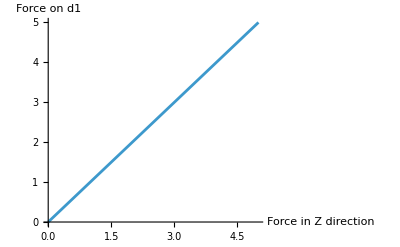

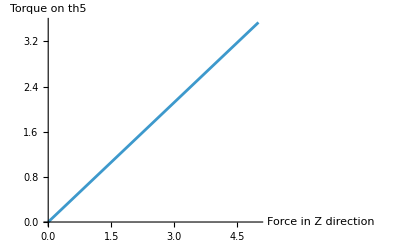

```mathematica
(*EXAMPLE!*)
tau = tau/.{th3[t]->Pi/4,th4[t]->Pi/4,th5[t]->Pi/4,d1[t]->1,d2[t]->1,L3->1,L4->1,L5->1,L6->1}; (*<---CONDITIONS*)
tau//MatrixForm
tau = tau/.{fx->0,fy->0,gy->0,gz->0};
tau // MatrixForm
tplot = {tau[[1]],tau[[5]]}
Plot[tau[[1]], {fz, 0, 5},AxesLabel -> {"Force in Z direction", "Force on d1"}]
Plot[tau[[5]], {fz, 0, 5},AxesLabel -> {"Force in Z direction", "Torque on th5"}]
```

{fx,fy,fz,gy,gz}

(fz
-fy
gz+fy (L4 Cos[th3[t]]+L6 Cos[th3[t]+th4[t]] Sin[th5[t]])+fx (-L4 Sin[th3[t]]-L6 Sin[th3[t]+th4[t]] Sin[th5[t]])
gz+fy L6 Cos[th3[t]+th4[t]] Sin[th5[t]]-fx L6 Sin[th3[t]+th4[t]] Sin[th5[t]]
gy+fx L6 Cos[th3[t]+th4[t]] Cos[th5[t]]+fy L6 Cos[th5[t]] Sin[th3[t]+th4[t]]+fz L6 Sin[th5[t]])

(fz
-fy
-√2 fx+fy/(√2)+gz
-fx/(√2)+gz
fy/(√2)+fz/(√2)+gy)

(0
-fy
fy/(√2)
0
fy/(√2))

{-fy,fy/(√2),fy/(√2)}

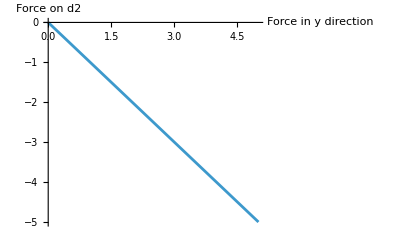

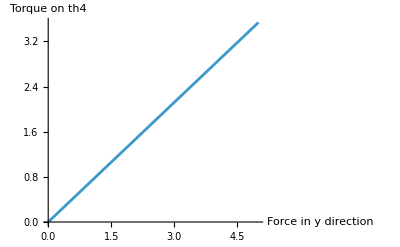

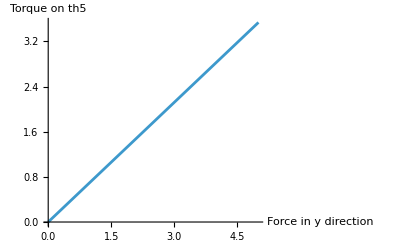

```mathematica
Fee = {fx,fy,fz,gy,gz}
tau = JT.Fee;
tau//MatrixForm
(*EXAMPLE!*)
tau = tau/.{th3[t]->Pi/4,th4[t]->Pi/4,th5[t]->Pi/4,d1[t]->1,d2[t]->1,L3->1,L4->1,L5->1,L6->1}; (*<---CONDITIONS*)
tau//MatrixForm
tau = tau/.{fx->0,fz->0,gy->0,gz->0};
tau // MatrixForm
tplot = {tau[[2]],tau[[3]],tau[[5]]}
Plot[tau[[2]], {fy, 0, 5},AxesLabel -> {"Force in y direction", "Force on d2"}]
Plot[tau[[3]], {fy, 0, 5},AxesLabel -> {"Force in y direction", "Torque on th4"}]
Plot[tau[[5]], {fy, 0, 5},AxesLabel -> {"Force in y direction", "Torque on th5"}]
```